#### Valores experimentales del silicio

```mathematica
hb=6.582119569*10^(-16);
```

```mathematica
datos0=Import["C:\\Users\\Poh\\Documents\\GitHub\\Tesis-de-Licenciatura\\Programas\\ParteIm.csv"];
(*Se eliminan los encabezados de los datos*)
datos1=Drop[datos0,1];
(*Se interpolan los datos de la parte imaginaria*)
parteIm=Drop[datos1[[All,2]],{1,20}];
(*Se toma a la primera columna como el vector de energía*)
omega=Drop[datos1[[All,1]],{1,20}];
```

```mathematica
parteReKK1=kkrebook[omega,parteIm];
parteImKK1=kkimbook[omega,parteReKK1];
parteReKK2=kkrebook[omega,parteImKK1];
prueba=selfconsbook[omega,parteReKK1,parteIm,100,0.6];
```

Set::setraw: Cannot assign to raw object 0.55.

Set::setraw: Cannot assign to raw object 0.6.

Set::setraw: Cannot assign to raw object 0.65.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

Set::setraw: Cannot assign to raw object 0.55.

Set::setraw: Cannot assign to raw object 0.6.

Set::setraw: Cannot assign to raw object 0.65.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

Set::setraw: Cannot assign to raw object 0.55.

Set::setraw: Cannot assign to raw object 0.6.

Set::setraw: Cannot assign to raw object 0.65.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

Set::setraw: Cannot assign to raw object 0.55.

Set::setraw: Cannot assign to raw object 0.6.

Set::setraw: Cannot assign to raw object 0.65.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

```mathematica
parteRepruebaInterp=Interpolation[Transpose[{omega,parteReKK1}]];
```

```mathematica
jaja=Table[{w,parteRepruebaInterp[w]},{w,0.56,6,0.01}];
```

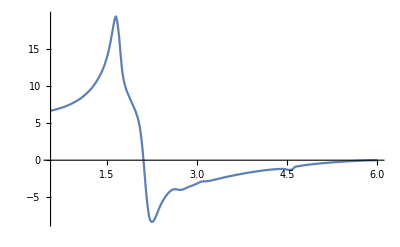

```mathematica
Plot[parteRepruebaInterp[x],{x,0.56,6}]
```

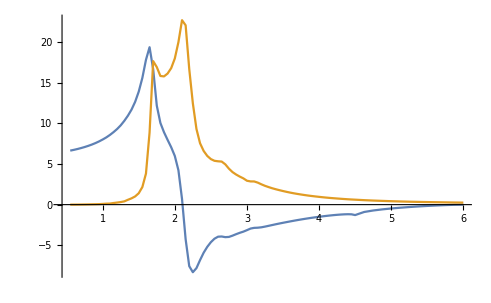

```mathematica
ListLinePlot[{Transpose[{omega,parteReKK1}],Transpose[{omega,parteIm}]},PlotRange->All]
```

```mathematica
ListLinePlot[{Style[Transpose[{omega,prueba[[1]]}],Dashed],Style[Transpose[{omega,prueba[[2]]}],Dashed],parteReKKPV,parteImPV,Transpose[{omega,parteReKK1}],jaja},PlotRange->All]
```

ListLinePlot::lpn: {{{0.55,5.81237},{0.6,6.28573},{0.65,6.53019},{0.7,6.72041},{0.75,6.89558},{0.8,7.07061},{0.85,7.25369},{0.9,7.45157},{0.95,7.67019},{1.,7.9122},«82»},{{0.55,-«19»},«9»,«82»},{},«1»,{«1»},{{0.56,6.65822},{0.57,6.67619},{0.58,6.69462},{0.59,6.71352},{0.6,6.7329},{0.61,6.75274},{0.62,6.77305},{0.63,6.79384},{0.64,6.81511},{0.65,6.83687},«535»}} is not a list of numbers or pairs of numbers.

ListLinePlot[{{{0.55,5.81237},{0.6,6.28573},{0.65,6.53019},{0.7,6.72041},{0.75,6.89558},{0.8,7.07061},{0.85,7.25369},{0.9,7.45157},{0.95,7.67019},{1,7.9122},{1.05,8.17799},{1.1,8.48579},{1.15,8.83401},{1.2,9.22179},{1.25,9.67835},{1.3,10.2272},{1.35,10.8571},{1.4,11.5974},{1.45,12.5379},{1.5,13.7612},{1.55,15.3656},{1.6,17.4077},{1.65,18.743},{1.7,16.2403},{1.75,12.1199},{1.8,10.0183},{1.85,8.84044},{1.9,7.86848},{1.95,6.9264},{2,5.81132},{2.05,4.02993},{2.1,0.6238},{2.15,-4.01316},{2.2,-7.16633},{2.25,-7.96688},{2.3,-7.56332},{2.35,-6.67165},{2.4,-5.82341},{2.45,-5.13708},{2.5,-4.5883},{2.55,-4.17672},{2.6,-3.93667},{2.65,-3.90441},{2.7,-3.96726},{2.75,-3.93438},{2.8,-3.78695},{2.85,-3.61224},{2.9,-3.45001},{2.95,-3.3058},{3,-3.12765},{3.05,-2.9416},{3.1,-2.8542},{3.15,-2.82678},{3.2,-2.77525},{3.25,-2.69152},{3.3,-2.59743},{3.35,-2.50115},{3.4,-2.40534},{3.45,-2.31365},{3.5,-2.2252},{3.55,-2.13929},{3.6,-2.05465},{3.65,-1.97179},{3.7,-1.8921},{3.75,-1.81595},{3.8,-1.74304},{3.85,-1.67257},{3.9,-1.605},{3.95,-1.54101},{4,-1.48037},{4.05,-1.42243},{4.1,-1.36655},{4.15,-1.3135},{4.2,-1.2644},{4.25,-1.21942},{4.3,-1.17833},{4.35,-1.1411},{4.4,-1.10855},{4.45,-1.08208},{4.5,-1.05081},{4.625,-0.739294},{4.75,-0.58159},{4.875,-0.461007},{5,-0.360875},{5.125,-0.274558},{5.25,-0.198944},{5.375,-0.132219},{5.5,-0.0733136},{5.625,-0.0213401},{5.75,0.0241135},{5.875,0.0629233},{6,0.0922885}},{{0.55,-2.42938},{0.6,-1.89195},{0.65,-1.58782},{0.7,-1.37975},{0.75,-1.22213},{0.8,-1.09487},{0.85,-0.987656},{0.9,-0.894565},{0.95,-0.808945},{1,-0.723212},{1.05,-0.636093},{1.1,-0.562006},{1.15,-0.451156},{1.2,-0.343881},{1.25,-0.227499},{1.3,-0.0801397},{1.35,0.155325},{1.4,0.407204},{1.45,0.739832},{1.5,1.26308},{1.55,2.19192},{1.6,4.05578},{1.65,8.52966},{1.7,15.2652},{1.75,15.4895},{1.8,14.9295},{1.85,14.9824},{1.9,15.3701},{1.95,16.045},{2,17.1473},{2.05,18.8337},{2.1,20.7613},{2.15,20.0377},{2.2,15.78},{2.25,12.0545},{2.3,9.18366},{2.35,7.44589},{2.4,6.43778},{2.45,5.78313},{2.5,5.35617},{2.55,5.10423},{2.6,4.98262},{2.65,4.87677},{2.7,4.55075},{2.75,4.08036},{2.8,3.6805},{2.85,3.37838},{2.9,3.12405},{2.95,2.89826},{3,2.64097},{3.05,2.53245},{3.1,2.48566},{3.15,2.34378},{3.2,2.15233},{3.25,1.97345},{3.3,1.8187},{3.35,1.6753},{3.4,1.54916},{3.45,1.43242},{3.5,1.32358},{3.55,1.22094},{3.6,1.12412},{3.65,1.03546},{3.7,0.953347},{3.75,0.87674},{3.8,0.804021},{3.85,0.734959},{3.9,0.670611},{3.95,0.609238},{4,0.549895},{4.05,0.491496},{4.1,0.434242},{4.15,0.379001},{4.2,0.323801},{4.25,0.266382},{4.3,0.204151},{4.35,0.133789},{4.4,0.0485703},{4.45,-0.0702285},{4.5,-0.300601},{4.625,-0.0159995},{4.75,0.0534265},{4.875,0.0829669},{5,0.0941792},{5.125,0.0976405},{5.25,0.0962684},{5.375,0.0925679},{5.5,0.0862152},{5.625,0.0767144},{5.75,0.0628773},{5.875,0.0405252},{6,-0.00310417}},parteReKKPV,parteImPV,{{0.55,6.64071},{0.6,6.7329},{0.65,6.83687},{0.7,6.95291},{0.75,7.08205},{0.8,7.22577},{0.85,7.38624},{0.9,7.56727},{0.95,7.77325},{1,8.00556},{1.05,8.26305},{1.1,8.56568},{1.15,8.91034},{1.2,9.29448},{1.25,9.75004},{1.3,10.3025},{1.35,10.9365},{1.4,11.6825},{1.45,12.6392},{1.5,13.8983},{1.55,15.5795},{1.6,17.8002},{1.65,19.3548},{1.7,16.6433},{1.75,12.1733},{1.8,10.0426},{1.85,8.90209},{1.9,7.95967},{1.95,7.05238},{2,5.98273},{2.05,4.22749},{2.1,0.687719},{2.15,-4.25529},{2.2,-7.56341},{2.25,-8.30668},{2.3,-7.80441},{2.35,-6.81652},{2.4,-5.90844},{2.45,-5.18796},{2.5,-4.61578},{2.55,-4.18733},{2.6,-3.93971},{2.65,-3.91732},{2.7,-3.99776},{2.75,-3.96901},{2.8,-3.81399},{2.85,-3.63217},{2.9,-3.46603},{2.95,-3.32145},{3,-3.13746},{3.05,-2.94179},{3.1,-2.85615},{3.15,-2.83593},{3.2,-2.78684},{3.25,-2.702},{3.3,-2.60665},{3.35,-2.50942},{3.4,-2.41281},{3.45,-2.32081},{3.5,-2.23227},{3.55,-2.14645},{3.6,-2.06188},{3.65,-1.97914},{3.7,-1.89979},{3.75,-1.82422},{3.8,-1.7521},{3.85,-1.68253},{3.9,-1.61608},{3.95,-1.55356},{4,-1.49474},{4.05,-1.43901},{4.1,-1.38572},{4.15,-1.3359},{4.2,-1.29103},{4.25,-1.25169},{4.3,-1.21834},{4.35,-1.19244},{4.4,-1.17848},{4.45,-1.18981},{4.5,-1.28298},{4.625,-0.903685},{4.75,-0.720603},{4.875,-0.584516},{5,-0.473212},{5.125,-0.378156},{5.25,-0.295467},{5.375,-0.22297},{5.5,-0.159465},{5.625,-0.104062},{5.75,-0.0566352},{5.875,-0.0183938},{6,0.0014656}},{{0.56,6.65822},{0.57,6.67619},{0.58,6.69462},{0.59,6.71352},{0.6,6.7329},{0.61,6.75274},{0.62,6.77305},{0.63,6.79384},{0.64,6.81511},{0.65,6.83687},{0.66,6.85908},{0.67,6.88178},{0.68,6.90498},{0.69,6.92869},{0.7,6.95291},{0.71,6.97765},{0.72,7.00291},{0.73,7.02873},{0.74,7.0551},{0.75,7.08205},{0.76,7.10956},{0.77,7.13767},{0.78,7.16639},{0.79,7.19575},{0.8,7.22577},{0.81,7.2564},{0.82,7.28773},{0.83,7.3198},{0.84,7.35263},{0.85,7.38624},{0.86,7.42066},{0.87,7.45594},{0.88,7.49211},{0.89,7.52921},{0.9,7.56727},{0.91,7.60642},{0.92,7.64659},{0.93,7.68777},{0.94,7.72999},{0.95,7.77325},{0.96,7.81764},{0.97,7.86308},{0.98,7.90955},{0.99,7.95705},{1.,8.00556},{1.01,8.05441},{1.02,8.10442},{1.03,8.15576},{1.04,8.20858},{1.05,8.26305},{1.06,8.32006},{1.07,8.37886},{1.08,8.43941},{1.09,8.50169},{1.1,8.56568},{1.11,8.63133},{1.12,8.69864},{1.13,8.76759},{1.14,8.83817},{1.15,8.91034},{1.16,8.98299},{1.17,9.05747},{1.18,9.13404},{1.19,9.21296},{1.2,9.29448},{1.21,9.37906},{1.22,9.46671},{1.23,9.55762},{1.24,9.65199},{1.25,9.75004},{1.26,9.85327},{1.27,9.96026},{1.28,10.0709},{1.29,10.185},{1.3,10.3025},{1.31,10.4218},{1.32,10.5446},{1.33,10.6712},{1.34,10.8017},{1.35,10.9365},{1.36,11.0736},{1.37,11.2159},{1.38,11.3643},{1.39,11.5196},{1.4,11.6825},{1.41,11.854},{1.42,12.0348},{1.43,12.2254},{1.44,12.4266},{1.45,12.6392},{1.46,12.863},{1.47,13.0999},{1.48,13.3507},{1.49,13.6166},{1.5,13.8983},{1.51,14.197},{1.52,14.5136},{1.53,14.8489},{1.54,15.2039},{1.55,15.5795},{1.56,16.0191},{1.57,16.4706},{1.58,16.9244},{1.59,17.3708},{1.6,17.8002},{1.61,18.2796},{1.62,18.7036},{1.63,19.0433},{1.64,19.27},{1.65,19.3548},{1.66,19.0735},{1.67,18.6417},{1.68,18.0793},{1.69,17.4065},{1.7,16.6433},{1.71,15.7588},{1.72,14.8368},{1.73,13.9101},{1.74,13.0113},{1.75,12.1733},{1.76,11.6032},{1.77,11.1159},{1.78,10.7005},{1.79,10.3464},{1.8,10.0426},{1.81,9.76062},{1.82,9.51192},{1.83,9.29016},{1.84,9.089},{1.85,8.90209},{1.86,8.70297},{1.87,8.51048},{1.88,8.3233},{1.89,8.14013},{1.9,7.95967},{1.91,7.78172},{1.92,7.6036},{1.93,7.42372},{1.94,7.24051},{1.95,7.05238},{1.96,6.86818},{1.97,6.6733},{1.98,6.46356},{1.99,6.23476},{2.,5.98273},{2.01,5.72169},{2.02,5.42444},{2.03,5.08219},{2.04,4.68613},{2.05,4.22749},{2.06,3.6501},{2.07,3.00437},{2.08,2.29337},{2.09,1.52013},{2.1,0.687719},{2.11,-0.285845},{2.12,-1.29123},{2.13,-2.30414},{2.14,-3.30026},{2.15,-4.25529},{2.16,-5.07747},{2.17,-5.82681},{2.18,-6.49587},{2.19,-7.07722},{2.2,-7.56341},{2.21,-7.87504},{2.22,-8.09462},{2.23,-8.23272},{2.24,-8.29989},{2.25,-8.30668},{2.26,-8.28155},{2.27,-8.21268},{2.28,-8.10615},{2.29,-7.96803},{2.3,-7.80441},{2.31,-7.62759},{2.32,-7.43586},{2.33,-7.23376},{2.34,-7.02581},{2.35,-6.81652},{2.36,-6.62507},{2.37,-6.43767},{2.38,-6.25519},{2.39,-6.0785},{2.4,-5.90844},{2.41,-5.75059},{2.42,-5.59994},{2.43,-5.45616},{2.44,-5.31894},{2.45,-5.18796},{2.46,-5.06181},{2.47,-4.94155},{2.48,-4.82715},{2.49,-4.71857},{2.5,-4.61578},{2.51,-4.5174},{2.52,-4.42507},{2.53,-4.33909},{2.54,-4.25974},{2.55,-4.18733},{2.56,-4.12192},{2.57,-4.0641},{2.58,-4.01422},{2.59,-3.97264},{2.6,-3.93971},{2.61,-3.92113},{2.62,-3.91058},{2.63,-3.90709},{2.64,-3.90966},{2.65,-3.91732},{2.66,-3.93197},{2.67,-3.94903},{2.68,-3.96682},{2.69,-3.98363},{2.7,-3.99776},{2.71,-4.0013},{2.72,-4.00032},{2.73,-3.99471},{2.74,-3.98432},{2.75,-3.96901},{2.76,-3.94493},{2.77,-3.91659},{2.78,-3.88478},{2.79,-3.85032},{2.8,-3.81399},{2.81,-3.77841},{2.82,-3.7421},{2.83,-3.70539},{2.84,-3.66864},{2.85,-3.63217},{2.86,-3.5975},{2.87,-3.56351},{2.88,-3.53023},{2.89,-3.49773},{2.9,-3.46603},{2.91,-3.43734},{2.92,-3.40903},{2.93,-3.3806},{2.94,-3.35157},{2.95,-3.32145},{2.96,-3.28691},{2.97,-3.25103},{2.98,-3.21401},{2.99,-3.17608},{3.,-3.13746},{3.01,-3.09537},{3.02,-3.05378},{3.03,-3.01367},{3.04,-2.97601},{3.05,-2.94179},{3.06,-2.91728},{3.07,-2.89683},{3.08,-2.88005},{3.09,-2.86661},{3.1,-2.85615},{3.11,-2.84989},{3.12,-2.84549},{3.13,-2.8422},{3.14,-2.83927},{3.15,-2.83593},{3.16,-2.82864},{3.17,-2.82015},{3.18,-2.81038},{3.19,-2.7993},{3.2,-2.78684},{3.21,-2.77193},{3.22,-2.75578},{3.23,-2.73861},{3.24,-2.72062},{3.25,-2.702},{3.26,-2.68349},{3.27,-2.66464},{3.28,-2.6455},{3.29,-2.62615},{3.3,-2.60665},{3.31,-2.58728},{3.32,-2.56784},{3.33,-2.54838},{3.34,-2.5289},{3.35,-2.50942},{3.36,-2.48992},{3.37,-2.47047},{3.38,-2.45112},{3.39,-2.43189},{3.4,-2.41281},{3.41,-2.39407},{3.42,-2.37552},{3.43,-2.35713},{3.44,-2.33889},{3.45,-2.32081},{3.46,-2.30285},{3.47,-2.28502},{3.48,-2.26732},{3.49,-2.24974},{3.5,-2.23227},{3.51,-2.21494},{3.52,-2.1977},{3.53,-2.18055},{3.54,-2.16347},{3.55,-2.14645},{3.56,-2.12942},{3.57,-2.11244},{3.58,-2.09552},{3.59,-2.07867},{3.6,-2.06188},{3.61,-2.04514},{3.62,-2.02848},{3.63,-2.01192},{3.64,-1.99547},{3.65,-1.97914},{3.66,-1.96299},{3.67,-1.94697},{3.68,-1.9311},{3.69,-1.91537},{3.7,-1.89979},{3.71,-1.88439},{3.72,-1.86913},{3.73,-1.85402},{3.74,-1.83905},{3.75,-1.82422},{3.76,-1.80955},{3.77,-1.79501},{3.78,-1.78059},{3.79,-1.76629},{3.8,-1.7521},{3.81,-1.73796},{3.82,-1.72393},{3.83,-1.71001},{3.84,-1.69621},{3.85,-1.68253},{3.86,-1.66896},{3.87,-1.65553},{3.88,-1.64223},{3.89,-1.62908},{3.9,-1.61608},{3.91,-1.60327},{3.92,-1.59061},{3.93,-1.57811},{3.94,-1.56576},{3.95,-1.55356},{3.96,-1.54152},{3.97,-1.52962},{3.98,-1.51786},{3.99,-1.50624},{4.,-1.49474},{4.01,-1.48337},{4.02,-1.47211},{4.03,-1.46097},{4.04,-1.44994},{4.05,-1.43901},{4.06,-1.42812},{4.07,-1.41734},{4.08,-1.40668},{4.09,-1.39614},{4.1,-1.38572},{4.11,-1.37543},{4.12,-1.36529},{4.13,-1.35532},{4.14,-1.34551},{4.15,-1.3359},{4.16,-1.32651},{4.17,-1.31732},{4.18,-1.30835},{4.19,-1.29958},{4.2,-1.29103},{4.21,-1.2827},{4.22,-1.2746},{4.23,-1.26673},{4.24,-1.25909},{4.25,-1.25169},{4.26,-1.24449},{4.27,-1.23755},{4.28,-1.23087},{4.29,-1.22446},{4.3,-1.21834},{4.31,-1.21242},{4.32,-1.20683},{4.33,-1.20162},{4.34,-1.19681},{4.35,-1.19244},{4.36,-1.18827},{4.37,-1.18468},{4.38,-1.18178},{4.39,-1.17968},{4.4,-1.17848},{4.41,-1.17691},{4.42,-1.17681},{4.43,-1.17863},{4.44,-1.18281},{4.45,-1.18981},{4.46,-1.20009},{4.47,-1.21409},{4.48,-1.23228},{4.49,-1.25509},{4.5,-1.28298},{4.51,-1.29843},{4.52,-1.31005},{4.53,-1.31666},{4.54,-1.31709},{4.55,-1.31014},{4.56,-1.29464},{4.57,-1.2694},{4.58,-1.23324},{4.59,-1.18498},{4.6,-1.12344},{4.61,-1.04742},{4.62,-0.955756},{4.63,-0.893587},{4.64,-0.874296},{4.65,-0.856146},{4.66,-0.839061},{4.67,-0.822964},{4.68,-0.807779},{4.69,-0.79343},{4.7,-0.77984},{4.71,-0.766932},{4.72,-0.754631},{4.73,-0.74286},{4.74,-0.731543},{4.75,-0.720603},{4.76,-0.708281},{4.77,-0.696248},{4.78,-0.684493},{4.79,-0.673005},{4.8,-0.661772},{4.81,-0.650784},{4.82,-0.640027},{4.83,-0.629492},{4.84,-0.619167},{4.85,-0.60904},{4.86,-0.5991},{4.87,-0.589336},{4.88,-0.579645},{4.89,-0.570019},{4.9,-0.560546},{4.91,-0.55122},{4.92,-0.542037},{4.93,-0.532994},{4.94,-0.524085},{4.95,-0.515306},{4.96,-0.506653},{4.97,-0.498121},{4.98,-0.489707},{4.99,-0.481405},{5.,-0.473212},{5.01,-0.465061},{5.02,-0.457012},{5.03,-0.449063},{5.04,-0.441212},{5.05,-0.433457},{5.06,-0.425796},{5.07,-0.418228},{5.08,-0.410749},{5.09,-0.403358},{5.1,-0.396054},{5.11,-0.388833},{5.12,-0.381695},{5.13,-0.374626},{5.14,-0.367623},{5.15,-0.360699},{5.16,-0.35385},{5.17,-0.347077},{5.18,-0.340378},{5.19,-0.333752},{5.2,-0.327198},{5.21,-0.320714},{5.22,-0.314301},{5.23,-0.307955},{5.24,-0.301678},{5.25,-0.295467},{5.26,-0.289308},{5.27,-0.283213},{5.28,-0.277183},{5.29,-0.271216},{5.3,-0.265312},{5.31,-0.25947},{5.32,-0.25369},{5.33,-0.247971},{5.34,-0.242311},{5.35,-0.236712},{5.36,-0.231172},{5.37,-0.22569},{5.38,-0.220264},{5.39,-0.214893},{5.4,-0.209579},{5.41,-0.204321},{5.42,-0.199119},{5.43,-0.193973},{5.44,-0.188882},{5.45,-0.183845},{5.46,-0.178863},{5.47,-0.173934},{5.48,-0.169058},{5.49,-0.164235},{5.5,-0.159465},{5.51,-0.154736},{5.52,-0.150059},{5.53,-0.145434},{5.54,-0.14086},{5.55,-0.136338},{5.56,-0.131868},{5.57,-0.127449},{5.58,-0.123081},{5.59,-0.118765},{5.6,-0.1145},{5.61,-0.110286},{5.62,-0.106124},{5.63,-0.102003},{5.64,-0.0979255},{5.65,-0.0938996},{5.66,-0.0899263},{5.67,-0.0860061},{5.68,-0.0821399},{5.69,-0.078328},{5.7,-0.0745713},{5.71,-0.0708702},{5.72,-0.0672254},{5.73,-0.0636376},{5.74,-0.0601073},{5.75,-0.0566352},{5.76,-0.0531161},{5.77,-0.0496604},{5.78,-0.0462729},{5.79,-0.0429584},{5.8,-0.0397214},{5.81,-0.0365668},{5.82,-0.0334993},{5.83,-0.0305234},{5.84,-0.0276441},{5.85,-0.0248659},{5.86,-0.0221935},{5.87,-0.0196318},{5.88,-0.0171853},{5.89,-0.0148589},{5.9,-0.0126571},{5.91,-0.0105848},{5.92,-0.00864655},{5.93,-0.00684717},{5.94,-0.00519134},{5.95,-0.00368375},{5.96,-0.00232913},{5.97,-0.00113217},{5.98,-0.0000975904},{5.99,0.000769903},{6.,0.0014656}}},PlotRange→All]

## Modelo de Drude

```mathematica
omegaMin=0.01; (*valor mínimo de energía*)
omegaMax=5; (*valor máximo de energía*)
omega1=Range[omegaMin,omegaMax,0.001]; (*rango de energías*)
omegaPAl=13.142; (*frecuencia de plasma Al*)
gammaAl=0.147; (*constante de amortuguamiento Al*)
```

```mathematica
(*Se define el modelo de drude*)
epsDrude[ω_,ωp_,γ_]:=1-((ωp)^2/(ω*(ω+ I γ)))
(*Se define la parte real y la imaginaria del índice de refracción*)
nImagDrude[energy_,omegaP_,gamma_]:=Im[Sqrt[epsDrude[energy,omegaP,gamma]]]
nReDrude[energy_,omegaP_,gamma_]:=Re[Sqrt[epsDrude[energy,omegaP,gamma]]]
```

```mathematica
alRealDrude=Table[{omega,nReDrude[omega,omegaPAl,gammaAl]},{omega,0.01,5,0.001}];
alImagDrude=Table[{omega,nImagDrude[omega,omegaPAl,gammaAl]},{omega,0.01,5,0.001}];
```

```mathematica
omegaconocida=4;
real1=nReDrude[4,omegaPAl,gammaAl];
```

```mathematica
Length[omega1]
Length[alImagDrude[[All,2]]]
```

4991

4991

```mathematica
sale=sskkrebook[omega1, alImagDrude[[All,2]],omegaconocida, real1];
```

```mathematica
parteReKK1Drude=kkrebook[omega1,alImagDrude[[All,2]]];
```

Set::setraw: Cannot assign to raw object {0.01,0.011,0.012,0.013,0.014,0.015,0.016,0.017,0.018,0.019,«4981»}.

Set::setraw: Cannot assign to raw object 250.175.

Set::setraw: Cannot assign to raw object 239.227.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

```mathematica
ListLinePlot[{Style[Transpose[{omega1,sale}],Dashed],alRealDrude,Transpose[{omega1,parteReKK1Drude}]},PlotRange->All]
```

Transpose::nmtx: The first two levels of {{0.01,0.011,0.012,0.013,0.014,0.015,0.016,0.017,0.018,0.019,«4981»},sskkrebook2[{0.01,0.011,0.012,0.013,0.014,0.015,0.016,0.017,0.018,0.019,«4981»},{250.175,239.227,229.699,221.31,213.85,«19»,«19»,195.628,190.607,185.994,«4981»},4,0.0633267]} cannot be transposed.

Transpose::nmtx: The first two levels of {{0.01,0.011,0.012,0.013,0.014,0.015,0.016,0.017,0.018,0.019,«4981»},sskkrebook2[{0.01,0.011,0.012,0.013,0.014,0.015,0.016,0.017,0.018,0.019,«4981»},{250.175,239.227,229.699,221.31,213.85,«19»,«19»,195.628,190.607,185.994,«4981»},4.,0.0633267]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListLinePlot::lpn: {{},{{0.01,233.736},{0.011,221.997},«7»,{0.019,163.504},«4981»},{{0.01,445.403},{0.011,355.613},{0.012,309.967},{0.013,279.609},{0.014,257.089},{0.015,239.343},{0.016,224.806},{0.017,212.568},{0.018,202.051},{0.019,192.867},«4981»}} is not a list of numbers or pairs of numbers.

#### Valores experimentales de eritrocitos

```mathematica
h=4.135667696*10^(-15); (*eV s*)
ℏ=6.582119569*10^(-16); (*eV s*)
c=3*^17 ;(*nm s^-1*)
```

```mathematica
datos0Im=Import["C:\\Users\\Poh\\Documents\\Tesis\\Refractive index\\28.7_k_ImN_Erythrocytes.csv"];
datos0Re=Import["C:\\Users\\Poh\\Documents\\Tesis\\Refractive index\\28.7_n_ReN_Erythrocytes.csv"];
(*Se eliminan los encabezados de los datos*)
datos1Im=Drop[datos0Im,1];
datos1Re=Drop[datos0Re,1];
datos2Im=h c/datos1Im[[All,1]];
datos2Re=h c/datos1Re[[All,1]];
(*Se interpolan los datos de la parte imaginaria*)
parteIm=Interpolation[Transpose[{datos2Im,datos1Im[[All,2]]}]];
parteRe=Interpolation[Transpose[{datos2Re,datos1Re[[All,2]]}]];
(*Se toma a la primera columna como el vector de energía*)
```

```mathematica
parteRe[3]
```

1.40941

```mathematica
parteImEq=Table[parteIm[x],{x,1.19,4.82,0.01}];
parteReEq=Table[parteRe[x],{x,1.19,4.82,0.01}];
omega=Range[1.19,4.82,0.01];
```

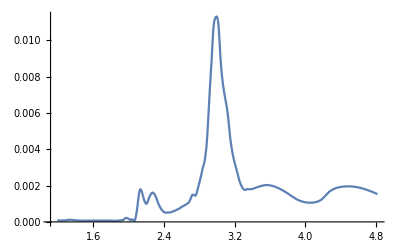

```mathematica
ListLinePlot[Transpose[{omega,parteImEq}],PlotRange->All]
```

```mathematica
parteImEq
```

{0.0000810247,0.0000817065,0.000081617,0.0000810258,0.0000802029,0.000079418,0.000078941,0.0000790416,0.0000799898,0.0000851701,0.0000915918,0.0000987298,0.000106079,0.000113136,0.000119396,0.000118213,0.000114745,0.000110054,0.000104477,0.0000983517,0.0000920154,0.0000858056,0.0000800598,0.0000772351,0.0000748558,0.0000728683,0.0000712449,0.0000699583,0.000068981,0.0000682857,0.0000678448,0.0000676311,0.0000676169,0.000067775,0.0000680778,0.000068498,0.000069008,0.0000695806,0.00007,0.00007,0.00007,0.00007,0.00007,0.00007,0.00007,0.00007,0.00007,0.00007,0.00007,0.00007,0.00007,0.00007,0.0000701506,0.0000704312,0.0000706582,0.0000708153,0.000070886,0.000070854,0.0000707029,0.0000704165,0.0000699055,0.0000676233,0.0000653681,0.0000632844,0.0000615171,0.0000602107,0.0000595101,0.0000595599,0.0000621552,0.0000680156,0.0000745216,0.0000814141,0.0000884345,0.0000953237,0.000101823,0.000107673,0.000151212,0.000198986,0.000218016,0.000214536,0.000194776,0.00016497,0.00013135,0.000100147,0.000138233,0.00012983,0.000106839,0.0000583023,0.0000890178,0.000252721,0.000522521,0.000888448,0.00129871,0.00165297,0.00179453,0.00178049,0.00164398,0.00146384,0.00129065,0.00113947,0.00103798,0.000991484,0.00104912,0.00116845,0.00131578,0.00142485,0.00151368,0.00157949,0.00161561,0.00160011,0.00154404,0.00146126,0.00135253,0.00122463,0.00109126,0.000965792,0.000864581,0.000775521,0.000698882,0.00063493,0.000583933,0.000546158,0.000521873,0.000511345,0.00051484,0.000516628,0.000515252,0.000518578,0.000526149,0.000537505,0.000552186,0.000569735,0.000589692,0.000609962,0.000630475,0.000652652,0.000676371,0.00070151,0.000727949,0.000755564,0.000789941,0.000824505,0.00085316,0.000878398,0.000902712,0.000928595,0.000958541,0.000995041,0.00102918,0.00106178,0.00114166,0.00125141,0.00137366,0.00149036,0.00149916,0.00147285,0.00144729,0.00145835,0.00157326,0.00176294,0.00195028,0.00213442,0.00232493,0.00252647,0.00274371,0.00297643,0.0031308,0.00333643,0.00363208,0.00405652,0.00467925,0.00551991,0.00640734,0.0073018,0.00811707,0.008883,0.00984561,0.0106499,0.0110526,0.0112158,0.0112982,0.0113153,0.0111643,0.0107525,0.00994937,0.0090752,0.00842139,0.00793131,0.00753408,0.00720503,0.00691993,0.00665183,0.00637498,0.00606365,0.00565022,0.00515751,0.00466408,0.00429419,0.00398067,0.00371344,0.00348313,0.00328039,0.00309586,0.00292017,0.00274397,0.00255789,0.00235257,0.00219921,0.00207182,0.00196474,0.00187895,0.00181544,0.00177516,0.00175911,0.00176825,0.00180357,0.00181001,0.00180073,0.00179708,0.0017985,0.00180439,0.00181419,0.0018273,0.00184315,0.00186116,0.00188074,0.00190133,0.00191844,0.00193292,0.0019473,0.00196135,0.00197485,0.00198755,0.00199923,0.00200967,0.00201862,0.00202585,0.00202996,0.00202857,0.00202523,0.00202,0.00201293,0.00200409,0.00199353,0.00198131,0.0019675,0.00195215,0.00193498,0.00191633,0.00189631,0.00187501,0.00185248,0.00182882,0.00180409,0.00177836,0.00175171,0.00172422,0.00169596,0.001667,0.00163741,0.00160728,0.00157667,0.0015441,0.00151092,0.00147774,0.00144469,0.00141194,0.00137962,0.0013479,0.00131692,0.00128683,0.00125778,0.00122993,0.00120708,0.00118579,0.00116607,0.00114795,0.00113145,0.00111657,0.00110335,0.0010918,0.00108195,0.0010738,0.00106739,0.00106272,0.00105982,0.00105871,0.00105941,0.00105953,0.00106059,0.00106381,0.00106934,0.0010773,0.00108783,0.00110107,0.00111714,0.00113617,0.00115831,0.00118367,0.0012124,0.00124902,0.00129405,0.00134129,0.00139027,0.00144056,0.00149169,0.00154321,0.00159469,0.00164566,0.0016822,0.00171488,0.00174499,0.00177261,0.00179785,0.00182078,0.00184151,0.00186011,0.00187669,0.00189132,0.00190411,0.00191514,0.00192451,0.00193229,0.00193859,0.00194349,0.00194708,0.00194946,0.00195264,0.00195565,0.00195753,0.00195831,0.00195801,0.00195666,0.00195428,0.00195091,0.00194655,0.00194124,0.00193501,0.00192788,0.00191988,0.00191102,0.00190135,0.00189087,0.00187962,0.00186762,0.0018549,0.00184149,0.0018274,0.00181266,0.00179731,0.00178135,0.00176483,0.00174777,0.00173018,0.0017121,0.00169355,0.00167456,0.00165515,0.00163534,0.00161517,0.00159466,0.00157383,0.0015527,0.00153132}

```mathematica
parteReKKPV=Table[{w,1.+(2/Pi)*NIntegrate[parteIm[x]*x/(x^2-w^2),{x,1.19,w,4.82},Method->"PrincipalValue"]},{w,omega[[2]],omega[[-2]],0.01}];
parteReKK1=kkrebook[omega,parteImEq];
parteImKK1=kkimbook[omega,parteReEq];
parteReKK2=kkrebook[omega,parteImKK1];
prueba=selfconsbook[omega,parteReKK1,parteImEq,100,0.6];
```

Set::setraw: Cannot assign to raw object {1.19,1.2,1.21,1.22,1.23,1.24,1.25,1.26,1.27,1.28,«354»}.

Set::setraw: Cannot assign to raw object 0.0000810247.

Set::setraw: Cannot assign to raw object 0.0000817065.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

Set::setraw: Cannot assign to raw object {1.19,1.2,1.21,1.22,1.23,1.24,1.25,1.26,1.27,1.28,«354»}.

Set::setraw: Cannot assign to raw object 1.4.

Set::setraw: Cannot assign to raw object 1.40024.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

Set::setraw: Cannot assign to raw object {1.19,1.2,1.21,1.22,1.23,1.24,1.25,1.26,1.27,1.28,«354»}.

Set::setraw: Cannot assign to raw object {-0.712473,-0.585259,-0.521609,-0.479148,-0.447219,-0.421253,-0.399574,-0.381666,-0.366286,-0.352391,«354»}.

Set::setraw: Cannot assign to raw object {1.19,1.2,1.21,1.22,1.23,1.24,1.25,1.26,1.27,1.28,«354»}.

Set::setraw: Cannot assign to raw object {1.00157,1.00155,1.00154,1.00154,1.00154,1.00154,1.00154,1.00154,1.00155,1.00155,«354»}.

Set::setraw: Cannot assign to raw object 0.0000810247.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

$Aborted

```mathematica
prueba[[1]]
```

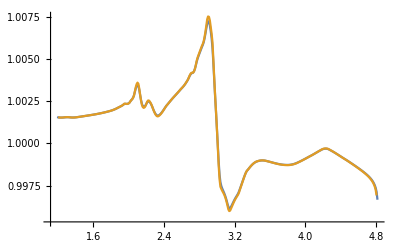

```mathematica
ListLinePlot[{Transpose[{omega,parteReKK1}],parteReKKPV},PlotRange->All]
```

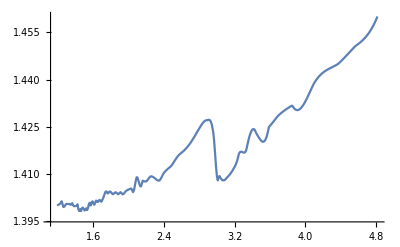

```mathematica
ListLinePlot[{Transpose[{omega,parteReEq}]},PlotRange->All]
```

```mathematica
parteRe[4]
```

1.43294

```mathematica
real1=parteRe[4];
omegaconocida=4;
sale=sskkrebook[omega, parteImEq,omegaconocida, real1];
```

Set::setraw: Cannot assign to raw object {1.19,1.2,1.21,1.22,1.23,1.24,1.25,1.26,1.27,1.28,«354»}.

Set::setraw: Cannot assign to raw object 0.0000810247.

Set::setraw: Cannot assign to raw object 0.0000817065.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

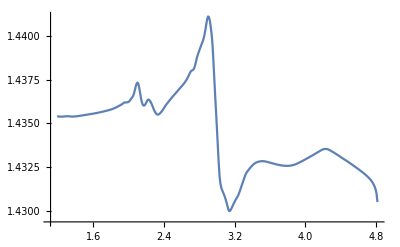

```mathematica
ListLinePlot[Transpose[{omega,sale}]]
```

#### Valores experimentales del oro

```mathematica
au=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Oro Johnson.csv"];
```

```mathematica
nau1=Drop[Drop[au,{51,101}],1];
kau1=Drop[au,{1,52}];
λAu=nau1[[All,1]]*1000; (*λ en um*)
ωAu=h c/λAu; (*eV*)
nau=nau1[[All,2]];
kau=kau1[[All,2]];
```

```mathematica
ωAu
```

{6.60298,6.47547,6.35279,6.22529,6.10281,5.98505,5.85512,5.73337,5.60389,5.48497,5.36403,5.23281,5.11418,4.98273,4.86358,4.74274,4.61398,4.49366,4.36252,4.24316,4.1233,3.99324,3.87235,3.74269,3.62248,3.50282,3.37238,3.25216,3.12204,3.00194,2.882,2.75161,2.63195,2.50192,2.38184,2.26158,2.13142,2.01151,1.88127,1.76111,1.64114,1.51102,1.39092,1.26087,1.14035,1.02031,0.890668,0.770621,0.640527}

```mathematica
nInterpFunction=Interpolation[Transpose[{ωAu,nau}]];
kInterpFunction=Interpolation[Transpose[{ωAu,kau}]];
```

```mathematica
nAu=Table[nInterpFunction[x],{x,0.65,6.6,0.01}];
kAu=Table[kInterpFunction[x],{x,0.65,6.6,0.01}];
energy=Range[0.65,6.6,0.01];
```

```mathematica
nInterpFunction[3]
```

1.45997

```mathematica
parteReKKAu=kkrebook[energy,kAu];
parteImKKAu=kkimbook[energy,parteReKKAu];
pruebaAu10=selfconsbook[energy,parteReKKAu,kAu,20,0.5];
pruebaSelf=sskkrebook[energy,kAu,3,nInterpFunction[3]];
```

Set::setraw: Cannot assign to raw object {0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,«586»}.

Set::setraw: Cannot assign to raw object 13.5607.

Set::setraw: Cannot assign to raw object 13.3351.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

Set::setraw: Cannot assign to raw object {0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,«586»}.

Set::setraw: Cannot assign to raw object {22.4847,17.8861,15.5244,13.9228,12.7085,11.731,10.9141,10.2139,9.6025,9.06121,«586»}.

Set::setraw: Cannot assign to raw object {0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,«586»}.

Set::setraw: Cannot assign to raw object {22.4847,17.8861,15.5244,13.9228,12.7085,11.731,10.9141,10.2139,9.6025,9.06121,«586»}.

Set::setraw: Cannot assign to raw object 13.5607.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

Set::setraw: Cannot assign to raw object {0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,«586»}.

Set::setraw: Cannot assign to raw object 13.5607.

Set::setraw: Cannot assign to raw object 13.3351.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

Set::setraw: Cannot assign to raw object {0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,«586»}.

Set::setraw: Cannot assign to raw object 13.5607.

Set::setraw: Cannot assign to raw object 13.3351.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

Set::setraw: Cannot assign to raw object {0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,«586»}.

Set::setraw: Cannot assign to raw object {22.4847,17.8861,15.5244,13.9228,12.7085,11.731,10.9141,10.2139,9.6025,9.06121,«586»}.

Set::setraw: Cannot assign to raw object {0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,«586»}.

Set::setraw: Cannot assign to raw object {22.4847,17.8861,15.5244,13.9228,12.7085,11.731,10.9141,10.2139,9.6025,9.06121,«586»}.

Set::setraw: Cannot assign to raw object 13.5607.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

2

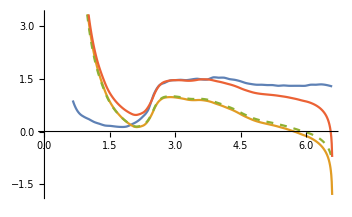

```mathematica
ListLinePlot[{Transpose[{energy,nAu}],Transpose[{energy,parteReKKAu}],Style[Transpose[{energy,pruebaAu10[[1]]}],Dashed],Transpose[{energy,pruebaSelf}]}]
```